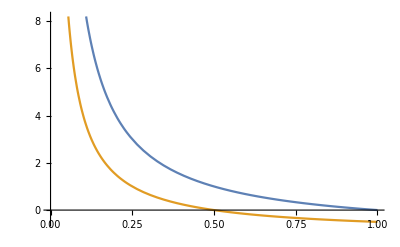

```mathematica
Plot[{1/α-1,1/(2α)-1},{α,0,1}]
```

```mathematica
Solve[β x^2+α x-1==0,x]
```

{{x→(-α-√(α^2+4 β))/(2 β)},{x→(-α+√(α^2+4 β))/(2 β)}}

```mathematica
Reduce[√(α^2+4 β)<(β+α^2)/α&&β>0,α]
```

β>0&&0<α<(√β)/(√2)

```mathematica
Reduce[α^4+4 β α^2<(β+α^2)^2&&β>0,α]
```

β>0&&-(√β)/(√2)<α<(√β)/(√2)

```mathematica
Plot3D[(√(α^2+4β)-(α+2β))/(2β),{α,0.01,1},{β,0.01,1},PlotRange->All]
```

-Graphics3D-

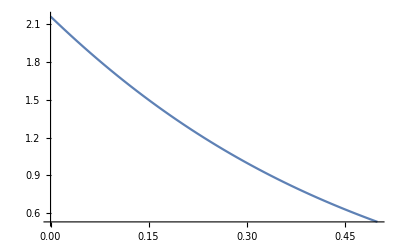

```mathematica
Plot[(√(α^2+4β)-(α+2β))/(2β)/.{β->0.1},{α,0,0.5}]
```

```mathematica
Limit[(√(α^2+4β)-(α+2β))/(2β),β->0,Assumptions->α>0]
```

-1+1/α

```mathematica
Simplify[Reduce[D[(√(α^2+4β)-(α+2β))/(2β),β]<0],α>0&&β>0]
```

True

```mathematica
D[√(α^2+4β)-(α+2β),β]
```

-2+2/(√(α^2+4 β))

```mathematica
Limit[(-2+2/(√(α^2+4 β)))/2,β->0]
```

-1+1/(√(α^2))

```mathematica
Simplify[(√(α^2+4β)-(α+2β))/(2β)/.{β->2 α^2},α>0]
```

-1+1/(2 α)

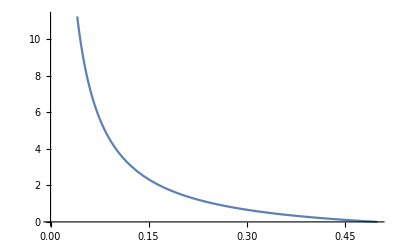

```mathematica
Plot[-1+1/(2 α),{α,0,0.5}]
```

```mathematica
Reduce[4 α β (1+2θ)+4(θ+β + 2β θ)^2<4β&&1>α>0&&β>0&&θ>0,θ]
```

0<α<1&&0<β<1-α&&0<θ<(-β-α β-2 β^2)/(1+2 β)^2+√((β-α β+4 β^2-2 α β^2+α^2 β^2+4 β^3)/(1+2 β)^4)

```mathematica
Simplify[(-β-α β-2 β^2)/(1+2 β)^2+√((β-α β+4 β^2-2 α β^2+α^2 β^2+4 β^3)/(1+2 β)^4),1>α>0&&β>0&&θ>0]
```

-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4)

```mathematica
Plot3D[{-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4),1/(4α)-1/2},{α,0,1},{β,0,1}]
```

-Graphics3D-

```mathematica
Simplify[Series[-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4),{α,0,2}],β>0]
```

(√β-β)/(1+2 β)-((√β+2 β) α)/(2 (1+2 β)^2)+(√β (-1+4 β) α^2)/(8 (1+2 β)^3)+O[α]^3

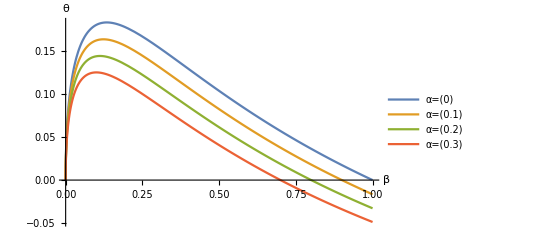

{α=[0],α=[0.1],α=[0.2],α=[0.3]}

```mathematica
Plot[Evaluate[-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4)/.α->{0,0.1,0.2,0.3}],{β,0,1},PlotLegends->"α="/@{0,0.1,0.2,0.3},AxesLabel->{β,θ}]
```

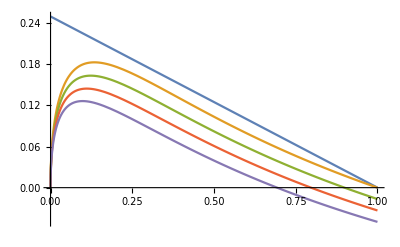

```mathematica
Plot[{1/4-1/4β,Evaluate[(√β-β)/(1+2 β)-((√β+2 β) α)/(2 (1+2 β)^2)/.α->{0,0.1,0.2,0.3}]},{β,0,1}]
```

```mathematica
Maximize[{-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4),0<α<1,0<β<1},{α,β}]
```

{(√(1/2 (2-√3)))/(3-√3)-(2-√3)/(2 (3-√3)),{α→0,β→1/2 (2-√3)}}

```mathematica
N[(√(1/2 (2-√3)))/(3-√3)-(2-√3)/(2 (3-√3))]
```

0.183013

```mathematica
Reduce[-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4)<1/(4α)-1/2&&0<α<1&&0<β<1]
```

(0<α<-1+√2&&0<β<1)||(α==-1+√2&&(0<β<1/2 (-1+2 (-1+√2)+2 (-1+√2)^2)-√(-(-1+√2)^2+2 (-1+√2)^3+(-1+√2)^4)||1/2 (-1+2 (-1+√2)+2 (-1+√2)^2)-√(-(-1+√2)^2+2 (-1+√2)^3+(-1+√2)^4)<β<1))||(-1+√2<α≤1/2&&(0<β<1/2 (-1+2 α+2 α^2)-√(-α^2+2 α^3+α^4)||1/2 (-1+2 α+2 α^2)+√(-α^2+2 α^3+α^4)<β<1))||(1/2<α<3/2 (-1+√2)&&1/2 (-1+2 α+2 α^2)+√(-α^2+2 α^3+α^4)<β<1)

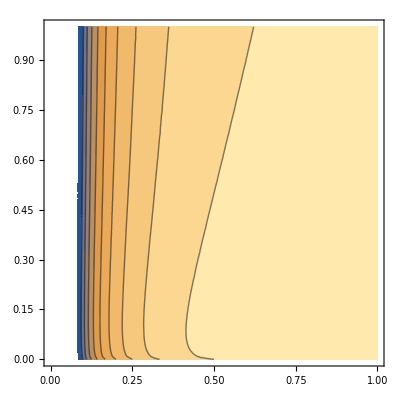

```mathematica
ContourPlot[-(β (1+α+2 β))/(1+2 β)^2+√((β (α^2 β-α (1+2 β)+(1+2 β)^2))/(1+2 β)^4)-(1/(4α)-1/2),{α,0,1},{β,0,1}]
```

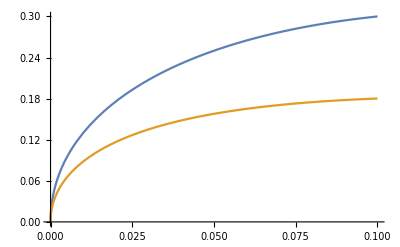

```mathematica
Plot[{√(2β-4β^2)-β,(√β-β)/(1+2 β)},{β,0,0.1}]
```

```mathematica
Simplify[Solve[2(α+θ β)(β+θ+θ β)==β,θ],
β>0]
```

{{θ→-(α+α β+β^2+√(-2 α β^2 (1+β)+α^2 (1+β)^2+β^2 (2+2 β+β^2)))/(2 β (1+β))},{θ→-(α+α β+β^2-√(-2 α β^2 (1+β)+α^2 (1+β)^2+β^2 (2+2 β+β^2)))/(2 β (1+β))}}

```mathematica
Simplify[Series[-(α+α β+β^2-√(-2 α β^2 (1+β)+α^2 (1+β)^2+β^2 (2+2 β+β^2)))/(2 β (1+β)),{α,0,1},{β,0,1}],β>0]
```

(1/(√2)+1/4 (-2-√2) β+O[β]^2)+(-1/(2 β)-1/(2 √2)+β/(4 √2)+O[β]^2) α+O[α]^2

```mathematica
Normal[(1/(√2)+1/4 (-2-√2) β+O[β]^2)+(-1/(2 β)-1/(2 √2)+β/(4 √2)+O[β]^2) α+O[α]^2]
```

1/(√2)+1/4 (-2-√2) β+α (-1/(2 √2)-1/(2 β)+β/(4 √2))

```mathematica
1/(√2)+1/4 (-2-√2) β+α (-1/(2 √2)-1/(2 β)+β/(4 √2))
```

1/(√2)+1/4 (-2-√2) β+α (-1/(2 √2)-1/(2 β)+β/(4 √2))

```mathematica
Simplify[1/(√2)+1/4 (-2-√2) β+α (-1/(2 √2)-1/(2 β)+β/(4 √2))]
```

1/(√2)-1/4 (2+√2) β+(α (-4-2 √2 β+√2 β^2))/(8 β)

```mathematica
Expand[1/(√2)-1/4 (2+√2) β+(α (-4-2 √2 β+√2 β^2))/(8 β)]
```

1/(√2)-α/(2 √2)-α/(2 β)-β/2-β/(2 √2)+(α β)/(4 √2)

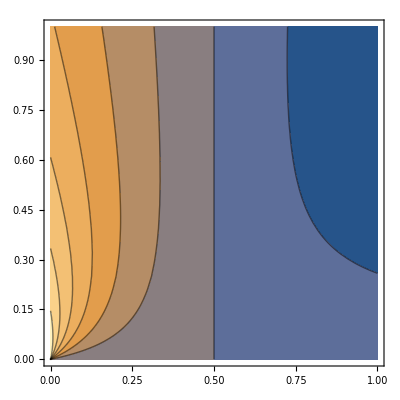

```mathematica
ContourPlot[-(α+α β+β^2-√(-2 α β^2 (1+β)+α^2 (1+β)^2+β^2 (2+2 β+β^2)))/(2 β (1+β)),{α,0,1},{β,0,1}]
```

```mathematica
{X,Y,Z}={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]}
```

{{{0,1},{1,0}},{{0,-ⅈ},{ⅈ,0}},{{1,0},{0,-1}}}

```mathematica
Xt=X.MatrixExp[-ⅈ RandomReal[{0,0.1},3].{X,Y,Z}]
```

{{0.0958037-0.0915565 ⅈ,0.990476+0.0373774 ⅈ},{0.990476-0.0373774 ⅈ,-0.0958037-0.0915565 ⅈ}}

```mathematica
Zt=Z.MatrixExp[-ⅈ RandomReal[{0,0.1},3].{X,Y,Z}]
```

{{0.991602-0.0860959 ⅈ,-0.0331431-0.0906328 ⅈ},{-0.0331431+0.0906328 ⅈ,-0.991602-0.0860959 ⅈ}}

```mathematica
KroneckerProduct[Transpose[Xt].Conjugate[Zt],X.Z]//MatrixForm//Chop
```

(0 | -0.0666668+0.17107 ⅈ | 0 | 0.973817-0.134057 ⅈ
0.0666668-0.17107 ⅈ | 0 | -0.973817+0.134057 ⅈ | 0
0 | -0.973817-0.134057 ⅈ | 0 | -0.0666668-0.17107 ⅈ
0.973817+0.134057 ⅈ | 0 | 0.0666668+0.17107 ⅈ | 0)

```mathematica
Eigensystem[KroneckerProduct[Transpose[Xt].Conjugate[Zt],X.Z]]//Chop
```

{{0.997775+0.0666668 ⅈ,0.997775-0.0666668 ⅈ,-0.997775+0.0666668 ⅈ,-0.997775-0.0666668 ⅈ},{{0.+0.541168 ⅈ,0.541168,-0.450871-0.0620675 ⅈ,-0.0620675+0.450871 ⅈ},{0.0620675+0.450871 ⅈ,-0.450871+0.0620675 ⅈ,0.541168,0.+0.541168 ⅈ},{-0.450871+0.0620675 ⅈ,0.0620675+0.450871 ⅈ,0.+0.541168 ⅈ,0.541168},{0.-0.541168 ⅈ,0.541168,0.450871+0.0620675 ⅈ,-0.0620675+0.450871 ⅈ}}}

```mathematica
KroneckerProduct[Conjugate[Zt].Transpose[Xt],Z.X]//MatrixForm//Chop
```

(0 | 0.0666668+0.00599146 ⅈ | 0 | 0.996849+0.042564 ⅈ
-0.0666668-0.00599146 ⅈ | 0 | -0.996849-0.042564 ⅈ | 0
0 | -0.996849+0.042564 ⅈ | 0 | 0.0666668-0.00599146 ⅈ
0.996849-0.042564 ⅈ | 0 | -0.0666668+0.00599146 ⅈ | 0)

```mathematica
Eigensystem[KroneckerProduct[Conjugate[Zt].Transpose[Xt],Z.X]]//Chop
```

{{-0.997775-0.0666668 ⅈ,-0.997775+0.0666668 ⅈ,0.997775+0.0666668 ⅈ,0.997775-0.0666668 ⅈ},{{-0.498043-0.0212657 ⅈ,-0.0212657+0.498043 ⅈ,0.+0.501499 ⅈ,0.501499},{0.501499,0.+0.501499 ⅈ,0.0212657+0.498043 ⅈ,-0.498043+0.0212657 ⅈ},{-0.0212657+0.498043 ⅈ,-0.498043-0.0212657 ⅈ,0.501499,0.+0.501499 ⅈ},{0.+0.501499 ⅈ,0.501499,-0.498043+0.0212657 ⅈ,0.0212657+0.498043 ⅈ}}}

```mathematica
Rx=ArrayReshape[{0.+0.5411680684002386 ⅈ,0.5411680684002393,-0.4508711022150456-0.062067470798678546 ⅈ,-0.0620674707986795+0.4508711022150442 ⅈ},{2,2}]
```

{{0.+0.541168 ⅈ,0.541168},{-0.450871-0.0620675 ⅈ,-0.0620675+0.450871 ⅈ}}

```mathematica
Rx=ArrayReshape[{0.+0.5411680684002386 ⅈ,0.5411680684002393,-0.4508711022150456-0.062067470798678546 ⅈ,-0.0620674707986795+0.4508711022150442 ⅈ},{2,2}]
```

```mathematica
Det[Rx]//Chop
```

0

```mathematica
Chop[Det[ArrayReshape[#,{2,2}]]]&/@Eigenvectors[KroneckerProduct[Conjugate[Zt].Transpose[Xt],Z.X]]
```

{0,0,0,0}

```mathematica
Eigenvalues[Z.X]
```

{ⅈ,-ⅈ}

```mathematica
Eigenvalues[Xt.ConjugateTranspose[Zt]]
```

{0.0666668-0.997775 ⅈ,0.0666668+0.997775 ⅈ}

```mathematica
N[Log[2]/4]
```

0.173287

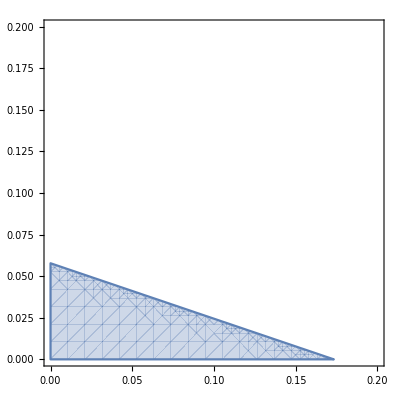

```mathematica
RegionPlot[α+3β<Log[2]/4&&α>0&&β>0,{α,0,0.2},{β,0,0.2}]
```

```mathematica
{{0,θ3,-θ2},{-θ3,0,θ1},{θ2,-θ1,0}}
```

{{0,θ3,-θ2},{-θ3,0,θ1},{θ2,-θ1,0}}

```mathematica
Eigenvalues[{{0,θ3,-θ2},{-θ3,0,θ1},{θ2,-θ1,0}}]
```

{0,-√(-θ1^2-θ2^2-θ3^2),√(-θ1^2-θ2^2-θ3^2)}

```mathematica
Norm[{{0,θ3,-θ2},{-θ3,0,θ1},{θ2,-θ1,0}}]
```

√(θ1 Conjugate[θ1]+θ2 Conjugate[θ2]+θ3 Conjugate[θ3])

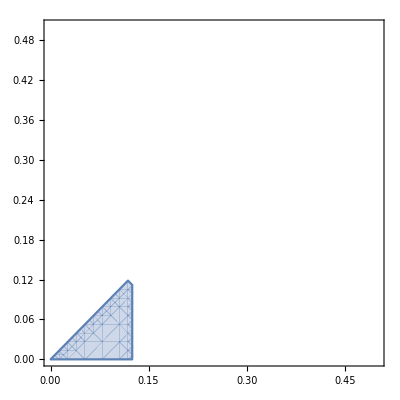

```mathematica
RegionPlot[α<1/8&&α>β>0,{α,0,0.5},{β,0,0.5}]
```